```mathematica
SetDirectory["/Users/jogh/research/ExQuareum/repo/predictions/EQLab"];
<<EQLab`

(*measurements*)
UserMeasure[]:=RandomReal[]//Which[#>0.5,1,True,-1]&
(*forecasts*)
predictivepowerA[xrandom_,meas_]:=Which[meas==1,1-xrandom^6,meas==-1,xrandom^6]
predictivepowerB[xrandom_,meas_]:=Which[meas==1,1-xrandom^2,meas==-1,xrandom^2]
predictivepowerC[xrandom_,meas_]:=Which[meas==1,1-xrandom,meas==-1,xrandom]
predictivepowerD[xrandom_,meas_]:=Which[meas==1,xrandom^(7/6) ,meas==-1,1-xrandom^(7/6) ]
predictivepowerE[xrandom_,meas_]:=Which[meas==1,xrandom^(3/2) ,meas==-1,1-xrandom^(3/2) ]

 PredictivePower=<|
"A"->predictivepowerA,
"B"->predictivepowerB,
"C"->predictivepowerC,
"D"->predictivepowerD,
"E"->predictivepowerE
|>;

(*g=<|
2->"A",
1->"B",
0->"C",
-1->"D",
-2->"E"
|>;
*)
npredictors=PredictivePower//Length;
nquestions=1000;


UserPredict[exp_,newquestion_]:=Table[RandomReal[{0.001,0.999}]//PredictivePower[i][#,newquestion[[2]]]&,{i,{"A","B","C","D","E"}}];


(*resolutions*)
Bias={
0.3,(*"A"*)
0.3,(*"B"*)
0.3,(*"C"*)
0.3,(*"D"*)
0.3    (*"E"*)
};
thresholdprobplus=0.9;
thresholdprobminus=1-thresholdprobplus;
UserResolve[exp_,newquestion_]:=Table[RandomReal[]//Which[#<Bias[[i]]&&newquestion[[2]]==1&&newquestion[[1,i]]<thresholdprobminus,-1,#<Bias[[i]]&&newquestion[[2]]==-1&&newquestion[[1,i]]>thresholdprobplus,1,True,newquestion[[2]]]&,{i,{1,2,3,4,5}}]

(*load user function into EQLab*)
SetUserFunctions[]
```

```mathematica
(*rcumul=Table[(EXPERIMENT[[1,All,6]]//Transpose//Part[#,i]&//getcumulative//Part[#,-1]&),{i,{1,2,3,4,5}}];
rcumulmax=Max[rcumul];
rcumulavg=Mean[rcumul];
winner=Position[rcumul,Max[rcumul]]//Flatten//Part[#,1]&
badrewarddifference=400;
If[rcumul[[1]]-rcumulavg>badrewarddifference,True,False]*)
```

```mathematica
RunExperiment[]
```

```mathematica
ShowPlots[All,"savgj"]
ShowPlots[All,"rcumul"]
```

-Graphics-

-Graphics-

```mathematica
nquestions=10;
```

```mathematica
RunExperiment[]
```

```mathematica
ShowPlots[-1,"rcumul"]
```

-Graphics-

```mathematica
EXPERIMENT[[-1,All,1]][[7;;8]]
```

{{0.00235161,0.05179,0.525806,0.231422,0.938627},{0.999906,0.988184,0.890518,0.0558782,0.0408512}}

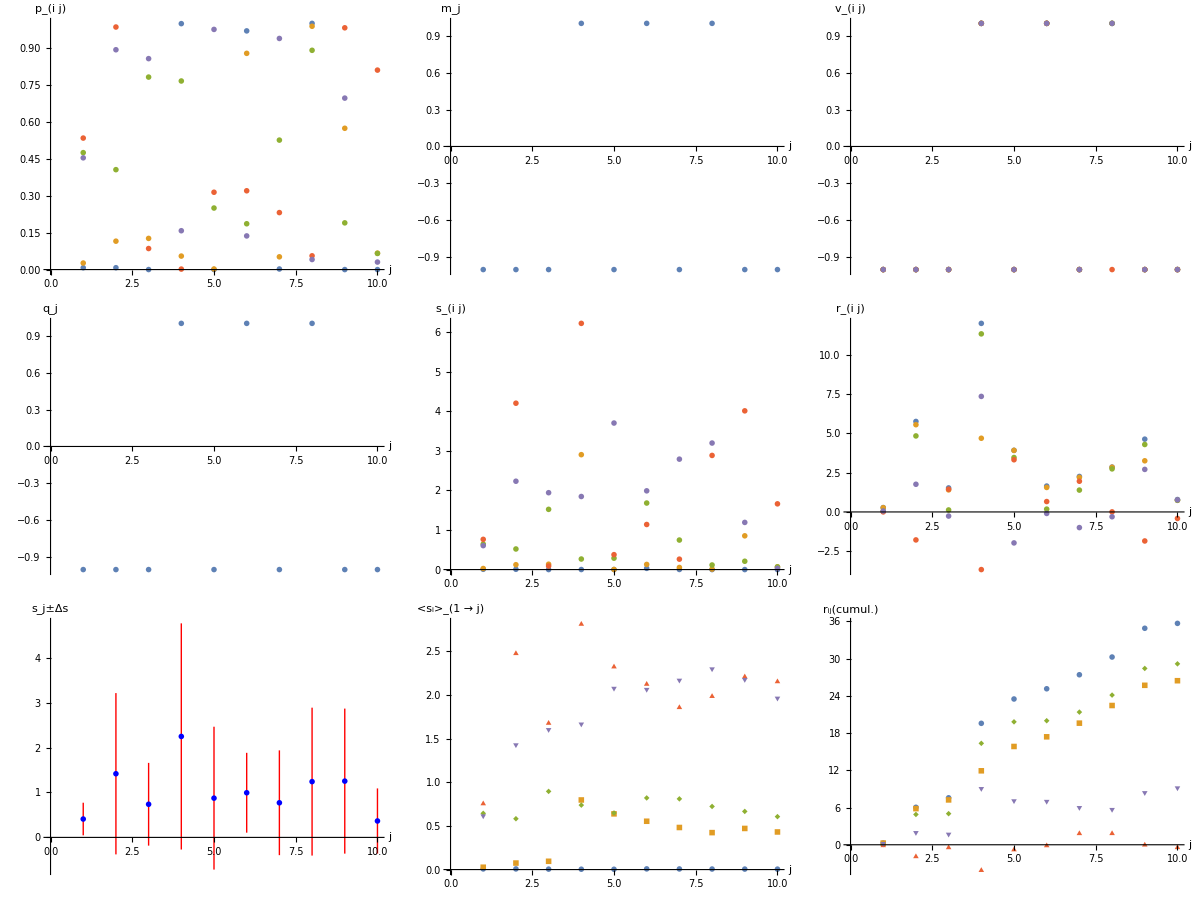

```mathematica
ShowPlots[-1]
```